Точность 0

Количество итераций 6.

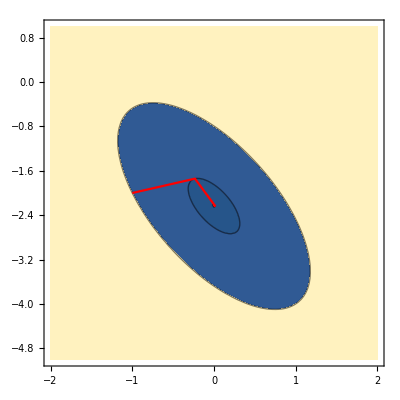

```mathematica
F[x_, y_]:=5 x^2+4x y+2 y^2+4 √5(x+y)+51;
(*alpha=128; (*8 128*)
F[x_, y_]:=alpha(x^2-y)^2+(x-1)^2;*)
Plot3D[F[x,y], {x, -10, 10}, {y,-10,10}];
FindMinimum[F[x, y], {x, -10}, {y, 10}];
SetDirectory[NotebookDirectory[]];
folderName = "grad6";(*grad fast*)
data=ReadList[StringJoin[folderName,"/points.txt"],Number,RecordLists->True];
iterCount = data[[1]][[1]];

inputFunc = StringJoin[folderName,"/func.txt"];
fValues = ReadList[inputFunc, Real];
iterCount = fValues[[1]];
fValues = Delete[fValues,1];

CoordLists = Delete[data, 1];
(*fValues = Table[F[CoordLists[[k]][[1]], CoordLists[[k]][[2]]], {k, 1, iterCount}];*)
Print["Точность ", 0];
Print["Количество итераций ",iterCount];
Show[ContourPlot[F[x,y], {x, -2, 2}, {y,-5,1}, Contours-> fValues], ListLinePlot[CoordLists, Joined->True, PlotStyle->{Red, PointSize[2]}, PlotRange->All]]
```